```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/NANOGrav2PBH"];
```

## Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

(√3)/ks

### log-normal

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0};
```

```mathematica
calPs[k_,ks_,As_,sg_]=As/(√(2π)sg)Exp[(-(Log[k]-Log[ks])^2)/(2 sg^2)];
Simplify[Integrate[calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

As

```mathematica
sigman[n_,ks_,As_,sg_]=Simplify[√Integrate[k^(2n)calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

√As ⅇ^(n^2 sg^2) ks^n

```mathematica
normN=Simplify[Sum[calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg]/.{As->1}
```

(3 (2+√ⅇ))/(√(2 ⅇ π))

```mathematica
psin[n_,r_,ks_,sg_]=Normal[Series[Simplify[1/(normN sigman[2,ks,As,sg]^2)Sum[Exp[2n logk] Sin[E^logk r]/(E^logk r)calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg],{sg,0,2}]]
```

(ks^(-5+2 n) Sin[ks r])/r-(ks^(-5+2 n) sg^2 (ks r Cos[ks r]-4 ks n r Cos[ks r]+15 Sin[ks r]+8 √ⅇ Sin[ks r]+4 n Sin[ks r]-4 n^2 Sin[ks r]+ks^2 r^2 Sin[ks r]))/((2+√ⅇ) r)

```mathematica
gamma3[sg_]=sigman[3,ks,As,sg]^2/(sigman[2,ks,As,sg]sigman[4,ks,As,sg])
```

ⅇ^(-2 sg^2)

```mathematica
Rb[ks_,sg_]=√3 sigman[3,ks,As,sg]/sigman[4,ks,As,sg]
```

(√3 ⅇ^(-7 sg^2))/ks

```mathematica
zetabar[r_,ks_,mu2_,kb_]=Normal[Series[Simplify[mu2/(1-gamma3[sg]^2)(psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])-mu2 kb^2 sigman[2,ks,As,sg]/(sigman[4,ks,As,sg]gamma3[sg](1-gamma3[sg]^2))(gamma3[sg]^2 psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])],{sg,0,2}]]/.{sg->0}
```

(mu2 (-4 ks (-kb^2+ks^2) r Cos[ks r]+((-12-10 √ⅇ) kb^2+(20+14 √ⅇ) ks^2) Sin[ks r]))/(4 (2+√ⅇ) ks^5 r)

```mathematica
zetaks[r_,ks_,mu2_]=zetabar[r,ks,mu2,ks]//Simplify
```

(mu2 Sin[ks r])/(ks^3 r)

```mathematica
zetax[x_,mu_]=zetaks[x/ks,ks,mu ks^2]//Simplify
```

(mu Sin[x])/x

```mathematica
CompactC[x_,mu_]=(1-(1+x D[zetax[x,mu], x])^2)/3//Simplify
```

(x^2-(x+mu x Cos[x]-mu Sin[x])^2)/(3 x^2)

```mathematica
rmcond[x_]=-x^2/mu(D[zetax[x,mu], x]+x D[D[zetax[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
xm=x/.FindRoot[rmcond[x]==0,{x,3}]
```

2.74371

```mathematica
Simplify[Solve[CompactC[x,mu]==Cth,mu]]/.{x->xm,Cth->0.267}
```

{{mu→0.521027},{mu→1.36026}}

```mathematica
Sin[xm]/xm
```

0.141221

```mathematica
xm/(6.4 10^-14)
```

4.28704×10^13

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

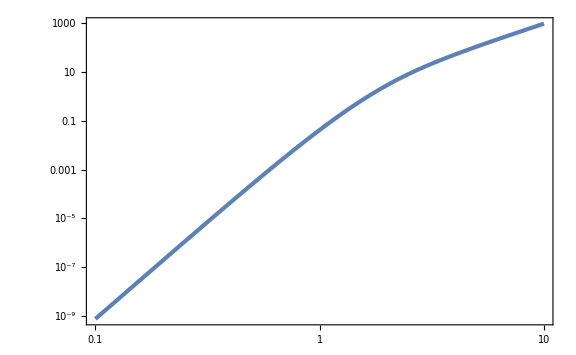

```mathematica
LogLogPlot[f[z],{z,0.1,10}]
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((1/0.12 1/(2.4 10^4)10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(π^2/30 3.38(2.725KineV)^4 0.28))^-1
```

7.10265×10^-18

```mathematica
((10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2 0.28))^-1
```

7.07168×10^-18

```mathematica
mu2[M_]=Log[M/10^20]/0.28;
```

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
mu2th=0.521;
```

```mathematica
fPBH[M_,As_]=M/10^20(f[mu2[M]/(√As)]PG[mu2[M],As])/(7.1 10^-18)UnitStep[mu2[M]-mu2th];
```

```mathematica
fPBH[1.18 10^20,2.8 10^-3]
```

1.35757×10^-6

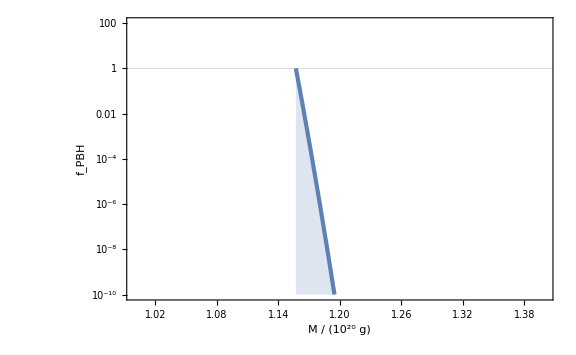

```mathematica
FigfPBH=LogPlot[fPBH[M 10^20,2.8 10^-3],{M,1,1.4},GridLines->{None,{1}},PlotRange->{{1,1.4},{10^-10,100}},Filling->Bottom,FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
sigmad2[R_,ks_,As_]=16/81 WTH[ks R]^2(ks R)^4 TrsT[ks R]^2 As//Simplify
```

(48 As (-ks R Cos[ks R]+Sin[ks R])^2 (√3 ks R Cos[(ks R)/(√3)]-3 Sin[(ks R)/(√3)])^2)/(ks^8 R^8)

```mathematica
sigmad2[ks^-1,ks,1]//N
```

0.150801

```mathematica
betaPBH[R_,ks_,As_]=1/2 Erfc[dth/(√(2sigmad2[R,ks,As]))]/.{dth->0.267 2};
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,ks_,As_]=betaPBH[R,ks,As]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,ks,As]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3}
```

{1.32039×10^19,1.32×10^-133}

```mathematica
fPBHPSList=Table[{MPBH[10^logR]/10^20,fPBHPS[10^logR,4.3 10^13,2.8 10^-3]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+1,0.01}];
```

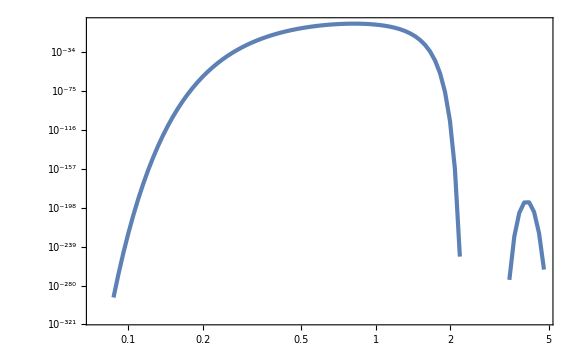

```mathematica
ListLogLogPlot[fPBHPSList]
```

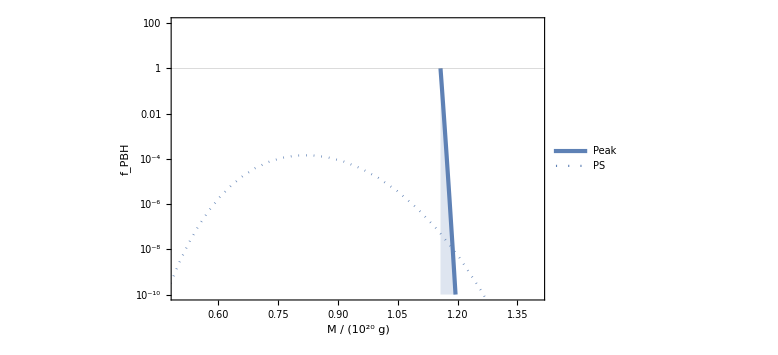

```mathematica
Show[LogPlot[{fPBH[M 10^20,2.8 10^-3],0},{M,1,1.4},GridLines->{None,{1}},PlotRange->{{0.5,1.4},{10^-10,100}},Filling->Bottom,FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},PlotLegends->Placed[{"Peak","PS"},{0.2,0.65}]],ListLogPlot[fPBHPSList,PlotStyle->{Color[1],Dotted}]]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

(2 √2)/3

2/kW

```mathematica
zetabar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetax[x_,mu_,kappa_]=zetabar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-((-384 mu+576 kappa^2 mu-72 mu x^2+96 kappa^2 mu x^2+x^4+24 mu (16-5 x^2+8 kappa^2 (-3+x^2)) Cos[x]+12 mu x (32-x^2+2 kappa^2 (-24+x^2)) Sin[x])^2)/x^8)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

4 (32+3 x^2-4 kappa^2 (12+x^2))+(-128+52 x^2-x^4+2 kappa^2 (96-40 x^2+x^4)) Cos[x]-x (128-11 x^2+6 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
FindRoot[xmcond[x,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->0.1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (4 (32+3 x^2-0.04 (12+x^2))+(-128+52 x^2-x^4+0.02 (96-40 Power[«2»]+x^4)) Cos[x]-x (128-11 x^2+0.06 (-32+3 Power[«2»])) Sin[x]==0) is less than WorkingPrecision (30.).

{x→5.3605653423668734007907946457}

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->30]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.23610391498593770655394732721

5.37014187909902279530303052317

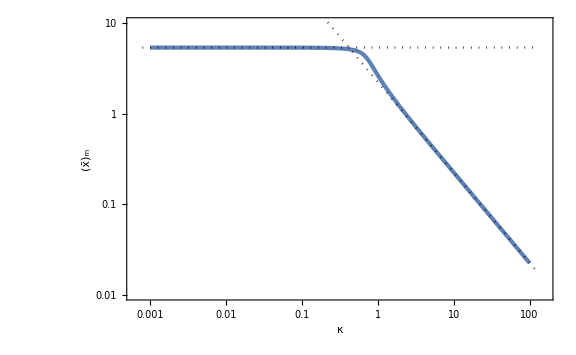

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.24/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==0.267,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

```mathematica
Solve[CompactC[5.37,mu,0]==0.267,mu]
```

{{mu→0.102313},{mu→0.26711}}

```mathematica
Normal[Series[mu/.Solve[Collect[Normal[Series[Simplify[CompactC[2.24/kappa,mu,kappa]],{kappa,∞,4}]],mu]==0.267,mu][[1]],{kappa,∞,2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.322681+0.2539/kappa^2+0.664695 kappa^2

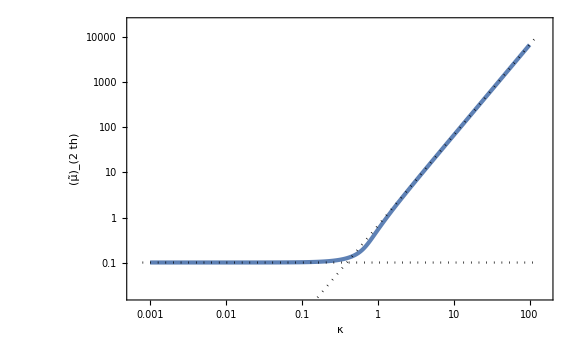

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.102,0.665 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

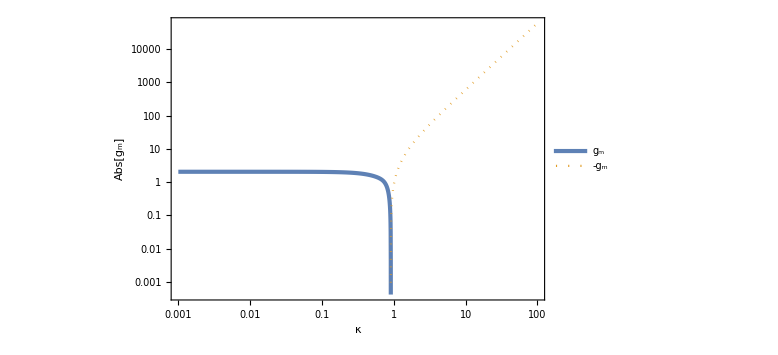

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

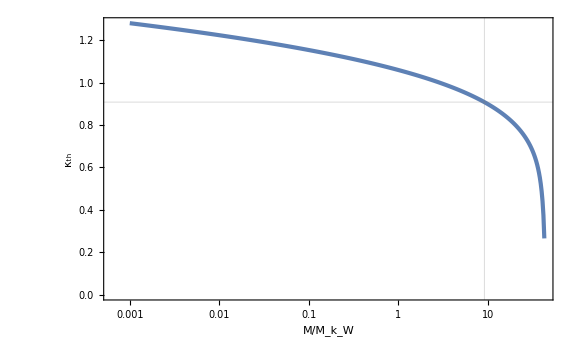

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
sigmamu=(kW^4/sigman[2,kW,As]^2)^(-1/2)//Simplify
```

(√As)/2

```mathematica
kappa2mean=sigman[3,kW,As]^2/sigman[2,kW,As]^2 1/kW^2//Simplify
```

2/3

```mathematica
sigmakappa=((mu^2 kW^4 kW^4)/(sigman[4,kW,As]^2(1-gamma3^2)))^(-1/2)//Simplify
```

(√As)/(6 √2 mu)

```mathematica
CC=1/kW^3(2 3^(3/2))/(2π)^(3/2)mu kW^2 kappa kW sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)(sigmamu sigmakappa)/(√(1-gamma3^2))kW^3//Simplify
```

(27 kappa)/(8 √2 π^(3/2))

```mathematica
zz=(mu kW^2 kappa^2 kW^2)/sigman[4,kW,As]//Simplify
```

(2 √2 kappa^2 mu)/(√As)

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

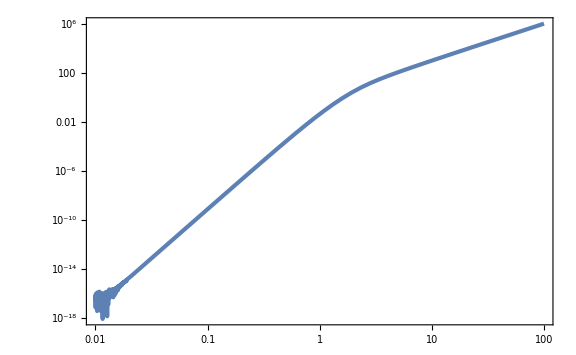

```mathematica
LogLogPlot[f[z],{z,10^-2,10^2}]
```

```mathematica
npk[mu_,kappa_,As_]=CC f[zz]PG[mu,0,sigmamu^2]PG[kappa^2,kappa2mean,sigmakappa^2]kappa//Simplify
```

(81 ⅇ^(-(6 (3-8 kappa^2+6 kappa^4) mu^2)/As) kappa^2 mu (ⅇ^(-(20 kappa^4 mu^2)/As) (-8/5+(4 kappa^4 mu^2)/As+ⅇ^((15 kappa^4 mu^2)/As) (8/5+(62 kappa^4 mu^2)/As)) √(2/(5 π))+(√2 kappa^2 mu (-3 As+8 kappa^4 mu^2) (Erf[(√5 kappa^2 mu)/(√As)]+Erf[(2 √5 kappa^2 mu)/(√As)]))/As^(3/2)))/(4 As π^(5/2))

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

8.37733×10^-75

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,1 10^-2]},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3]},{logM,1,2,10^-2}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{72.8698,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{72.2775,Null}

```mathematica
(*Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];*)
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

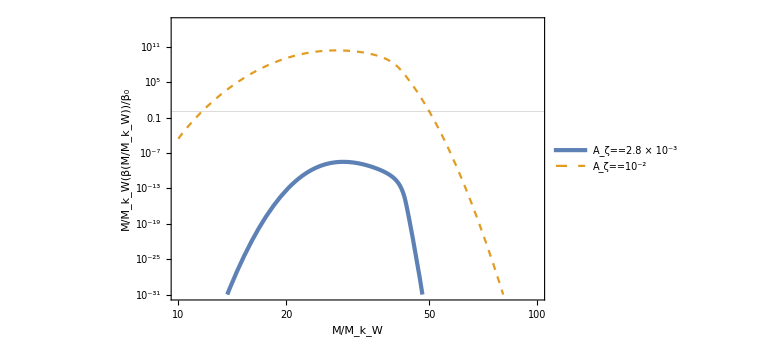

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.82,0.85}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,20},WorkingPrecision->30][[2]]
```

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(«1») MM)) is less than WorkingPrecision (30.).

3.11903354176128427117906107374×10^-9

FindMaximum::precw: The precision of the argument function (-(5.73049×10^15 10^(«1») MM)) is less than WorkingPrecision (30.).

28.8015410141772332872142088305

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2975.02 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2529.91 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2133.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

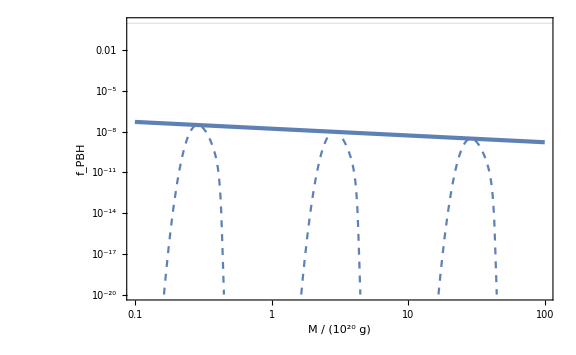

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
Integrand[z_]=WTH[k R]^2(k R)^4 TrsT[k R]^2/.{k->z/R}//Simplify
```

(243 (-z Cos[z]+Sin[z])^2 (√3 z Cos[z/(√3)]-3 Sin[z/(√3)])^2)/z^8

```mathematica
NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

5.36981

```mathematica
sigmad2[As_]=16/81 As NIntegrate[Integrand[z] 1/z,{z,0,10^4}]
```

1.0607 As

```mathematica
betaPBH[As_]=1/2 Erfc[dth/(√(2sigmad2[As]))]/.{dth->0.267 2};
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,As_]=betaPBH[As]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,As]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3}
```

{1.32039×10^19,2.18112×10^-7}

```mathematica
fPBHPSList=Table[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
```

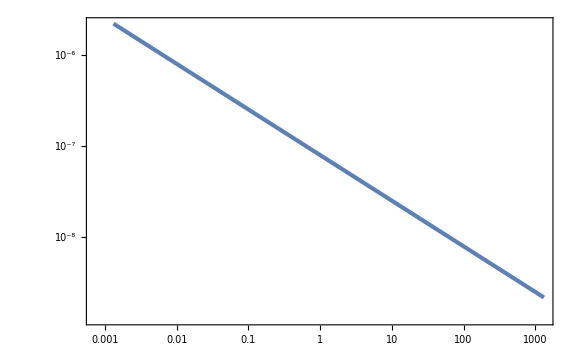

```mathematica
ListLogLogPlot[fPBHPSList]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2975.02 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2529.91 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2133.67 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

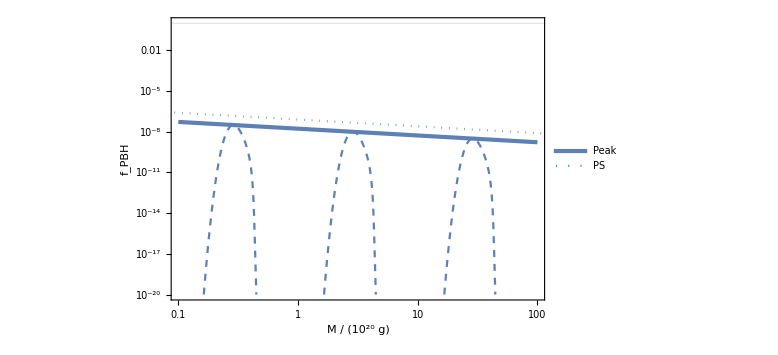

```mathematica
Show[LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2),0},{MM,0.1,100},PlotRange->{10^-20,1},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[{None,None,None,"Peak","PS"},{0.8,0.8}],FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}],ListLogLogPlot[fPBHPSList,PlotStyle->{Dotted}]]
```

### power law

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n≥1,ns>-2,As>0,kW>0,mu>0,kappa>0};
```

```mathematica
calPz[k_,As_,ks_,ns_]=As(k/ks)^ns;
```

```mathematica
sigman[n_,kW_,As_,ks_,ns_]=√Integrate[k^(2n)calPz[k,As,ks,ns] 1/k,{k,0,kW}]//Simplify
```

√((As ks^-ns kW^(2 n+ns))/(2 n+ns))

```mathematica
psin[n_,r_,kW_,ks_,ns_]=1/sigman[2,kW,As,ks,ns]^2 Integrate[k^(2n)Sin[k r]/(k r)calPz[k,As,ks,ns] 1/k,{k,0,kW}]//Simplify
```

(kW^(-4+2 n) (4+ns) HypergeometricPFQ[{n+ns/2},{3/2,1+n+ns/2},-1/4 kW^2 r^2])/(2 n+ns)

```mathematica
psin[1,r,kW,ks,ns]//Simplify
psin[2,r,kW,ks,ns]//Simplify
```

((4+ns) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2])/(kW^2 (2+ns))

HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2]

```mathematica
gamma3[ns_]=sigman[3,kW,As,ks,ns]^2/(sigman[2,kW,As,ks,ns]sigman[4,kW,As,ks,ns])//Simplify
Rb[kW_,ns_]=√3 sigman[3,kW,As,ks,ns]/sigman[4,kW,As,ks,ns]//Simplify
```

(√((4+ns) (8+ns)))/(6+ns)

(√3 √((8+ns)/(6+ns)))/kW

```mathematica
zetabar[r_,kW_,ns_,mu2_,kb_]=mu2/(1-gamma3[ns]^2)(psin[1,r,kW,ks,ns]-1/3 Rb[kW,ns]^2 psin[2,r,kW,ks,ns])-mu2 kb^2 sigman[2,kW,As,ks,ns]/(sigman[4,kW,As,ks,ns]gamma3[ns](1-gamma3[ns]^2))(gamma3[ns]^2 psin[1,r,kW,ks,ns]-1/3 Rb[kW,ns]^2 psin[2,r,kW,ks,ns])//Simplify
```

1/(4 kW^4)mu2 (6+ns)^2 ((kW^2 (4+ns) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2])/(2+ns)-(kW^2 (8+ns) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2])/(6+ns)-(kb^2 (8+ns) ((4+ns)^2 HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-1/4 kW^2 r^2]-(12+8 ns+ns^2) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-1/4 kW^2 r^2]))/((2+ns) (4+ns) (6+ns)))

```mathematica
zetax[x_,ns_,mu_,kappa_]=zetabar[x/kW,kW,ns,mu kW^2,kappa kW]//FullSimplify
```

(mu (6+ns) (-((4+ns)^2 (-6-ns+kappa^2 (8+ns)) HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4])/(2+ns)+(8+ns) (-4-ns+kappa^2 (6+ns)) HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]))/(4 (4+ns))

```mathematica
CompactC[x_,ns_,mu_,kappa_]=(1-(1+x D[zetax[x,ns,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-(1-1/(4 x)mu (6+ns) ((4+ns) (6+ns-kappa^2 (8+ns)) (x HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4]-Sin[x])+(8+ns) (-4-ns+kappa^2 (6+ns)) (x HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]-Sin[x])))^2)

```mathematica
xmcond[x_,ns_,kappa_]=(D[zetax[x,ns,mu,kappa], x]+x D[D[zetax[x,ns,mu,kappa], x], x])/mu//Simplify
```

-1/(4 x^2)(6+ns) (-2 (-4-ns+kappa^2 (8+ns)) x Cos[x]+(8+6 ns+ns^2) (-6-ns+kappa^2 (8+ns)) x HypergeometricPFQ[{1+ns/2},{3/2,2+ns/2},-x^2/4]-(32+12 ns+ns^2) (-4-ns+kappa^2 (6+ns)) x HypergeometricPFQ[{2+ns/2},{3/2,3+ns/2},-x^2/4]+2 (-44-19 ns-2 ns^2+kappa^2 (72+25 ns+2 ns^2)) Sin[x])

```mathematica
FindRoot[xmcond[x,-1/2,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->10^-1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

{x→5.58273667673438840904381471746}

```mathematica
xmList=Flatten[ParallelTable[{10^logk,ns,x/.FindRoot[xmcond[x,ns,10^logk]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]},{logk,-3,2,10^-1},{ns,-19/10,2,10^-1}],1];//AbsoluteTiming
```

{4.49837,Null}

```mathematica
xmint[kappa_,ns_]=Interpolation[xmList][kappa,ns];
```

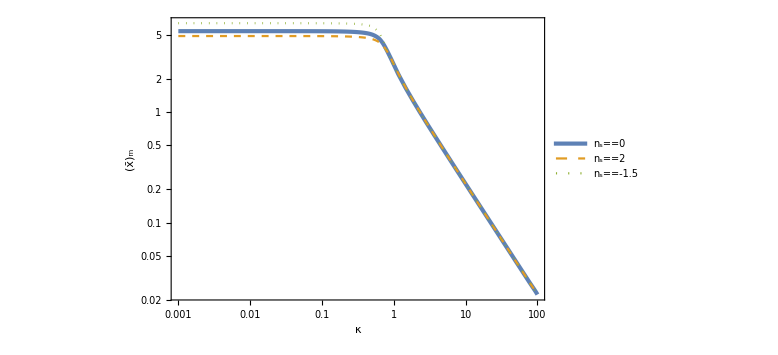

```mathematica
LogLogPlot[{xmint[kappa,0],xmint[kappa,2],xmint[kappa,-1.5]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.25,0.3}],FrameLabel->{κ,Subscript[OverBar[x], "m"]}]
```

```mathematica
Cmax[mu_,kappa_,ns_]=CompactC[xmint[kappa,ns],ns,mu,kappa];
```

```mathematica
muthList=Flatten[ParallelTable[{10^logk,ns,mu/.Solve[Cmax[mu,10^logk,ns]==0.267,mu][[1]]},{logk,-3,2,10^-1},{ns,-19/10,2,10^-1}],1];//AbsoluteTiming
```

{5.41555,Null}

```mathematica
muthint[kappa_,ns_]=Interpolation[muthList][kappa,ns];
```

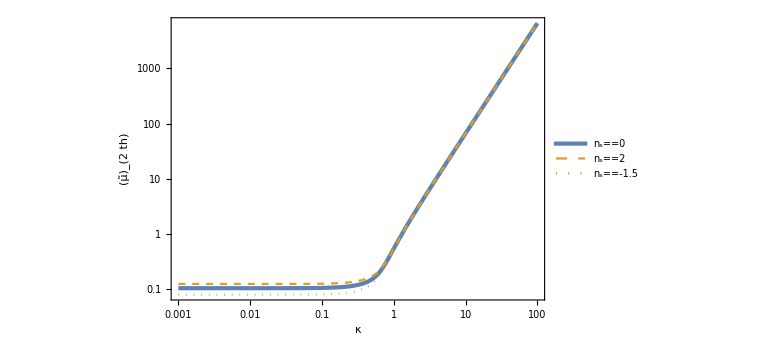

```mathematica
LogLogPlot[{muthint[kappa,0],muthint[kappa,2],muthint[kappa,-1.5]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],Dashed,Dotted},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.25,0.7}],FrameLabel->{κ,Subscript[OverTilde[μ], 2th]}]
```

```mathematica
gm[kappa_,ns_]=zetax[xmint[kappa,ns],ns,mu,kappa]/mu//Simplify;
```

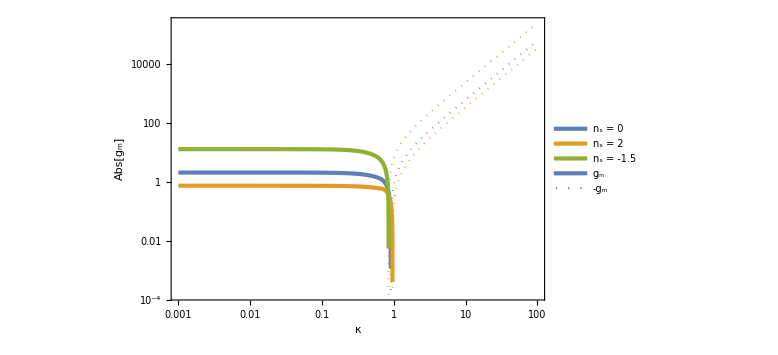

```mathematica
Show[LogLogPlot[{gm[kappa,0],-gm[kappa,0],gm[kappa,2],-gm[kappa,2],gm[kappa,-1.5],-gm[kappa,-1.5]},{kappa,10^-3,10^2},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted},{Color[3],AbsoluteThickness[3]},{Color[3],Dotted}},PlotLegends->Placed[LineLegend[{"n_s = 0",None,"n_s = 2",None,"n_s = -1.5",None},LegendLayout->"Row",LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.3,0.8}]],LogLogPlot[{0,0},{kappa,0.001,100},PlotStyle->{{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},PlotLegends->Placed[LineLegend[{"g_m",-"g_m"},LegendLayout->"Row",LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20],{0.3,0.7}]]]
```

```mathematica
kappacList=Table[{ns,kappa/.FindRoot[gm[kappa,ns]==0,{kappa,1}]},{ns,-19/10,2,10^-1}];//AbsoluteTiming
```

{0.900001,Null}

```mathematica
kappacint[ns_]=Interpolation[kappacList][ns];
```

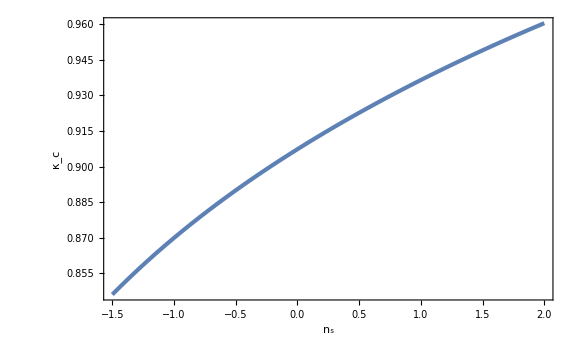

```mathematica
Plot[kappacint[ns],{ns,-1.5,2},FrameLabel->{Subscript[n, "s"],Subscript[κ, "c"]}]
```

```mathematica
MoMkW[mu_,kappa_,ns_]=xmint[kappa,ns]^2 Exp[2mu gm[kappa,ns]];
```

```mathematica
MContour0=Table[i,{i,-5,5,1/4}];
MContourm=Table[i,{i,-20,20}];
MContourp=Table[i,{i,-5,5,1/5}];
```

```mathematica
Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,0]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour0,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[0]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==0}}],ContourPlot[MoMkW[10^logm,10^logk,0]==MoMkW[muthint[10^-3,0],10^-3,0],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,0]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
FigMoMkWm=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,-1.5]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContourm,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[-1.5]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==-1.5}}],ContourPlot[MoMkW[10^logm,10^logk,-1.5]==MoMkW[muthint[10^-3,-1.5],10^-3,-1.5],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,-1.5]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
FigMoMkWp=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk,2]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContourp,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappacint[2]]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{{Subscript["log", 10] Subscript[OverTilde[μ], 2],None},{Row[{Subscript["log", 10]," ",κ}],Subscript[n, "s"]==2}}],ContourPlot[MoMkW[10^logm,10^logk,2]==MoMkW[muthint[10^-3,2],10^-3,2],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk,2]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
(*Export["MoMkW_m1,5.pdf",FigMoMkWm];
Export["MoMkW_p2.pdf",FigMoMkWp];*)
```

```mathematica
Mc[ns_]=MoMkW[0.1,kappacint[ns],ns];
Mth[ns_]=MoMkW[muthint[10^-3,ns],10^-3,ns];
```

```mathematica
Mc[-1.5]
Mth[-1.5]
Mc[2]
Mth[2]
```

11.1265

292.702

8.10472

28.1231

```mathematica
muM[kappa_,ns_,MM_]=1/(2gm[kappa,ns])Log[MM/xmint[kappa,ns]^2];
```

```mathematica
FindRoot[muM[kappa,-1.5,0.9Mth[-1.5]]==muthint[kappa,-1.5],{kappa,0.9kappacint[-1.5]}]
```

{kappa→0.555554}

```mathematica
FindRoot[muM[kappa,-1.5,0.001]==muthint[kappa,-1.5],{kappa,1.1kappacint[-1.5]}]
```

{kappa→1.02839}

```mathematica
FindRoot[muM[kappa,2,0.9Mth[2]]==muthint[kappa,2],{kappa,0.9kappacint[2]}]
```

{kappa→0.53093}

```mathematica
FindRoot[muM[kappa,2,0.001]==muthint[kappa,2],{kappa,1.1kappacint[2]}]
```

{kappa→1.43857}

```mathematica
FindRoot[muM[kappa,-1.5,100]==muthint[kappa,-1.5],{kappa,0.8kappacint[-1.5]},WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ((1.11111 Log[100/(InterpolatingFunction[«1»][kappa,-1.5])^2])/(-12.5 (-4.5+6.5 Power[«2»]) HypergeometricPFQ[{0.25},{3/2,1.25},-1/4 Power[«2»]]+6.5 (-2.5+4.5 Power[«2»]) HypergeometricPFQ[{1.25},{3/2,2.25},-1/4 Power[«2»]])==«1») is less than WorkingPrecision (30.).

{kappa→0.73822448377197264289745889825}

```mathematica
kappathList1=Flatten[ParallelTable[{ns,logM,kappa/.FindRoot[muM[kappa,ns,10^logM]==muthint[kappa,ns],{kappa,0.999kappacint[ns]}]},{ns,-19/10,2,10^-1},{logM,Log10[Mc[ns]]+10^-3,Log10[Mth[ns]],10^-2}],1];//AbsoluteTiming
```

{46.4885,Null}

```mathematica
kappathList2=Flatten[Table[{ns,logM,kappa/.FindRoot[muM[kappa,ns,10^logM]==muthint[kappa,ns],{kappa,1.001kappacint[ns]}]},{ns,-19/10,2,10^-1},{logM,-3,Log10[Mc[ns]],10^-1}],1];//AbsoluteTiming
```

{61.7697,Null}

```mathematica
kappathList=Sort[Join[kappathList1,kappathList2]];
```

```mathematica
kappathint[ns_,MM_]=Interpolation[kappathList][ns,Log10[MM]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction::femdmval: Input value {2.,1.44906} lies outside the range of data in the interpolating function.

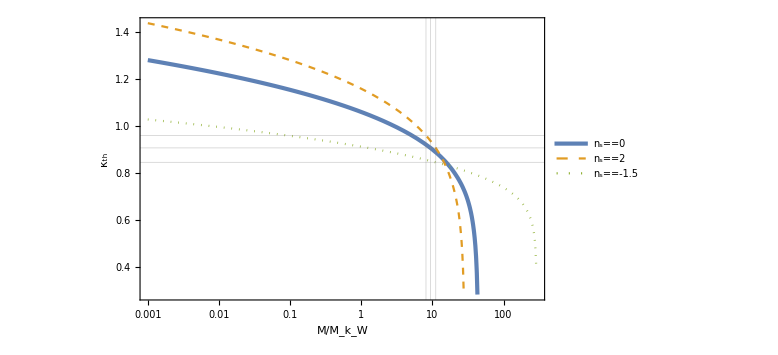

```mathematica
Show[LogLinearPlot[{kappathint[0,MM],0,0},{MM,10^-3,Mth[0]},GridLines->{{Mc[-1.5],Mc[0],Mc[2]},{kappacint[-1.5],kappacint[0],kappacint[2]}},PlotRange->{{10^-3,Mth[-1.5]},{kappathint[2,Mth[2]],kappathint[2,10^-3]}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},PlotLegends->Placed[{Subscript[n, "s"]==0,Subscript[n, "s"]==2,Subscript[n, "s"]==-1.5},{0.2,0.25}],PlotStyle->{AbsoluteThickness[3],Dashed,Dotted}],LogLinearPlot[kappathint[2,MM],{MM,10^-3,Mth[2]},PlotStyle->{Color[2],Dashed}],LogLinearPlot[kappathint[-1.5,MM],{MM,10^-3,Mth[-1.5]},PlotStyle->{Color[3],Dotted}]]
```

```mathematica
sigmamu=(kW^4/sigman[2,kW,As,ks,ns]^2)^(-1/2)/.{As->calPzW (kW/ks)^-ns}//Simplify
```

1/(√((4+ns)/calPzW))

```mathematica
kappa2mean=sigman[3,kW,As,ks,ns]^2/sigman[2,kW,As,ks,ns]^2 1/kW^2//Simplify
```

(4+ns)/(6+ns)

```mathematica
sigmakappa=((mu^2 kW^4 kW^4)/(sigman[4,kW,As,ks,ns]^2(1-gamma3[ns]^2)))^(-1/2)/.{As->calPzW (kW/ks)^-ns}//Simplify
```

2/(√((mu^2 (6+ns)^2 (8+ns))/calPzW))

```mathematica
CC=1/kW^3(2 3^(3/2))/(2π)^(3/2)mu kW^2 kappa kW sigman[4,kW,As,ks,ns]^2/(sigman[2,kW,As,ks,ns] sigman[3,kW,As,ks,ns]^3)(sigmamu sigmakappa)/(√(1-gamma3[ns]^2))kW^3/.{As->calPzW (kW/ks)^-ns}//Simplify
```

3 √(3/2) kappa ((6+ns)/(8 π+ns π))^(3/2)

```mathematica
zz=(mu kW^2 kappa^2 kW^2)/sigman[4,kW,As,ks,ns]/.{As->calPzW (kW/ks)^-ns}//Simplify
```

(kappa^2 mu)/(√(calPzW/(8+ns)))

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_,ks_,kW_,ns_]=CC f[zz]PG[mu,0,sigmamu^2]PG[kappa^2,kappa2mean,sigmakappa^2]kappa/.{calPzW->calPz[kW,As,ks,ns]}//Simplify;
```

```mathematica
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,kappacint[ns],kappathint[ns,MM]}]/;MM<Mc[ns]
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,kappathint[ns,MM],kappacint[ns]}]/;Mc[ns]<MM<Mth[ns]
nPBH[MM_,As_,ks_,kW_,ns_]:=NIntegrate[2gm[kappa,ns]npk[muM[kappa,ns,MM],kappa,As,ks,kW,ns],{kappa,0,kappacint[ns]}]/;MM>Mth[ns]
```

```mathematica
k20=1.56 10^13;
```

```mathematica
nPBHListRedp=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,√10 k20,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListRed0=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListRedm=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20/√10,-0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
```

{47.7665,Null}

{47.6731,Null}

{47.8111,Null}

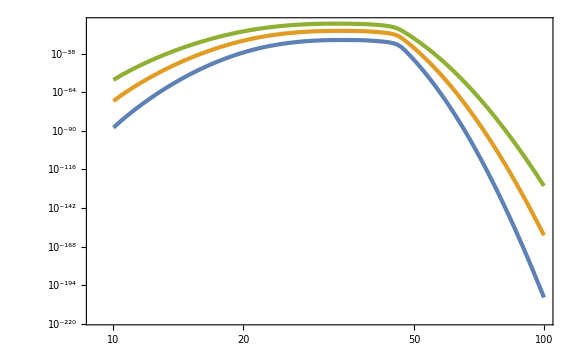

```mathematica
ListLogLogPlot[{nPBHListRedp,nPBHListRed0,nPBHListRedm}]
```

```mathematica
nPBHListBluep=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,√10 k20,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListBlue0=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
nPBHListBluem=ParallelTable[{10^logM,nPBH[10^logM,2.8 10^-3,k20,k20/√10,0.2]//Quiet},{logM,1,2,10^-2}];//AbsoluteTiming
```

{51.2338,Null}

{51.097,Null}

{51.1844,Null}

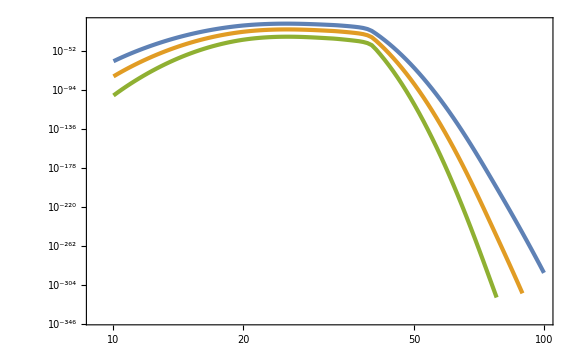

```mathematica
ListLogLogPlot[{nPBHListBluep,nPBHListBlue0,nPBHListBluem}]
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHListRedp=Map[Log10,nPBHListRedp,{2}]//Simplify;
LognPBHListRed0=Map[Log10,nPBHListRed0,{2}]//Simplify;
LognPBHListRedm=Map[Log10,nPBHListRedm,{2}]//Simplify;
```

```mathematica
nPBHintRedp[MM_]=10^(Interpolation[LognPBHListRedp][Log10[MM]]);
nPBHintRed0[MM_]=10^(Interpolation[LognPBHListRed0][Log10[MM]]);
nPBHintRedm[MM_]=10^(Interpolation[LognPBHListRedm][Log10[MM]]);
```

```mathematica
LognPBHListBluep=Map[Log10,nPBHListBluep,{2}]//Simplify;
LognPBHListBlue0=Map[Log10,nPBHListBlue0,{2}]//Simplify;
LognPBHListBluem=Map[Log10,nPBHListBluem,{2}]//Simplify;
```

```mathematica
nPBHintBluep[MM_]=10^(Interpolation[LognPBHListBluep][Log10[MM]]);
nPBHintBlue0[MM_]=10^(Interpolation[LognPBHListBlue0][Log10[MM]]);
nPBHintBluem[MM_]=10^(Interpolation[LognPBHListBluem][Log10[MM]]);
```

```mathematica
MkW[kW_]=10^20(kW/k20)^-2;
```

```mathematica
fPBHRedp[MM_]=(MkW[√10 k20]/10^20)^(-1/2)(MM MkW[k20]/MkW[√10 k20] nPBHintRedp[MM MkW[k20]/MkW[√10 k20]])/n2f;
fPBHRed0[MM_]=(MkW[k20]/10^20)^(-1/2)(MM nPBHintRed0[MM])/n2f;
fPBHRedm[MM_]=(MkW[k20/√10]/10^20)^(-1/2)(MM MkW[k20]/MkW[k20/√10] nPBHintRedm[MM MkW[k20]/MkW[k20/√10]])/n2f;
```

```mathematica
fPBHBluep[MM_]=(MkW[√10 k20]/10^20)^(-1/2)(MM MkW[k20]/MkW[√10 k20] nPBHintBluep[MM MkW[k20]/MkW[√10 k20]])/n2f;
fPBHBlue0[MM_]=(MkW[k20]/10^20)^(-1/2)(MM nPBHintBlue0[MM])/n2f;
fPBHBluem[MM_]=(MkW[k20/√10]/10^20)^(-1/2)(MM MkW[k20]/MkW[k20/√10] nPBHintBluem[MM MkW[k20]/MkW[k20/√10]])/n2f;
```

```mathematica
MmaxRedp=MM/.FindMaximum[fPBHRedp[MM],{MM,3},WorkingPrecision->30][[2]]
MmaxRed0=MM/.FindMaximum[fPBHRed0[MM],{MM,30}][[2]]
MmaxRedm=MM/.FindMaximum[fPBHRedm[MM],{MM,300}][[2]]
```

3.43898760913397611899994059905

33.795

332.638

```mathematica
fPBHmaxRedp=FindMaximum[fPBHRedp[MM],{MM,3},WorkingPrecision->30][[1]]
fPBHmaxRed0=FindMaximum[fPBHRed0[MM],{MM,30}][[1]]
fPBHmaxRedm=FindMaximum[fPBHRedm[MM],{MM,300}][[1]]
```

7.68187799382275832583332948823×10^-12

3.32861×10^-6

0.0742487

```mathematica
fPBHRedList=Map[Log10,{{MmaxRedp,fPBHmaxRedp},{MmaxRed0,fPBHmaxRed0},{MmaxRedm,fPBHmaxRedm}},{2}];
fPBHRedint[MM_]=10^(Interpolation[fPBHRedList][Log10[MM]]);
```

```mathematica
MmaxBluep=MM/.FindMaximum[fPBHBluep[MM],{MM,3},WorkingPrecision->30][[2]]
MmaxBlue0=MM/.FindMaximum[fPBHBlue0[MM],{MM,30},WorkingPrecision->30][[2]]
MmaxBluem=MM/.FindMaximum[fPBHBluem[MM],{MM,300},WorkingPrecision->50][[2]]
```

2.53603891095715268589213408005

25.430426591143034432750916966

254.88331693368291346403772199859109249398092270515

```mathematica
fPBHmaxBluep=FindMaximum[fPBHBluep[MM],{MM,3},WorkingPrecision->30][[1]]
fPBHmaxBlue0=FindMaximum[fPBHBlue0[MM],{MM,30},WorkingPrecision->30][[1]]
fPBHmaxBluem=FindMaximum[fPBHBluem[MM],{MM,300},WorkingPrecision->50][[1]]
```

5.82358813393036278090263216836×10^-6

1.16602367016177934833147031619×10^-12

5.2966402525789846961442416861162643296542679374004×10^-21

```mathematica
fPBHBlueList=Map[Log10,{{MmaxBluep,fPBHmaxBluep},{MmaxBlue0,fPBHmaxBlue0},{MmaxBluem,fPBHmaxBluem}},{2}];
fPBHBlueint[MM_]=10^(Interpolation[fPBHBlueList][Log10[MM]]);
```

```mathematica
fPBHflat[MM_]=3.1190335417612842711790610737385686790601101939361`30.*^-9(MM/(28.80154101417723328721420883047391386046`30.))^(-1/2);
```

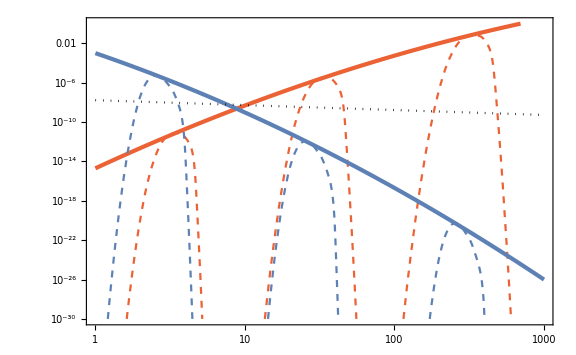

```mathematica
LogLogPlot[{fPBHRedp[MM]UnitStep[50-MM],fPBHRed0[MM],fPBHRedm[MM],fPBHRedint[MM],fPBHBluep[MM],fPBHBlue0[MM],fPBHBluem[MM],fPBHBlueint[MM],fPBHflat[MM]},{MM,1,10^3},PlotRange->{10^-30,1},PlotStyle->{{Color[4],Dashed},{Color[4],Dashed},{Color[4],Dashed},{Color[4],AbsoluteThickness[3]},{Color[1],Dashed},{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Black,Dotted}}]
```

#### Press-Schechter

```mathematica
WTH[z_]=3(Sin[z]-z Cos[z])/z^3;
TrsT[z_]=WTH[z/√3];
```

```mathematica
calPz[k,As,ks,ns]
```

As (k/ks)^ns

```mathematica
sigmad2[As_,ks_,ns_,R_]:=16/81 NIntegrate[calPz[k,As,ks,ns] WTH[k R]^2(k R)^4 TrsT[k R]^2 1/k,{k,0,10^4 R^-1}]
```

```mathematica
sigmad2[2.8 10^-3,k20,-0.2,1/k20]
```

0.00255182

```mathematica
betaPBH[As_,ks_,ns_,R_]:=1/2 Erfc[dth/(√(2sigmad2[As,ks,ns,R]))]/.{dth->0.267 2}
```

```mathematica
MPBH[R_]=10^20(R/(6.4 10^-14))^2;
```

```mathematica
fPBHPS[R_,As_,ks_,ns_]:=betaPBH[As,ks,ns,R]/(7.2 10^-16)(MPBH[R]/10^20)^(-1/2);
```

```mathematica
{MPBH[R],fPBHPS[R,As,ks,ns]}/.{R->ks^-1}/.{ks->4.3 10^13,As->2.8 10^-3,ns->0.2}
```

{1.32039×10^19,0.000264562}

```mathematica
fPBHPSListRed=ParallelTable[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3,k20,-0.2]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
fPBHPSListBlue=ParallelTable[{MPBH[10^logR]/10^20,fPBHPS[10^logR,2.8 10^-3,k20,0.2]},{logR,-Log10[4.3 10^13]-1,-Log10[4.3 10^13]+2,0.01}];
```

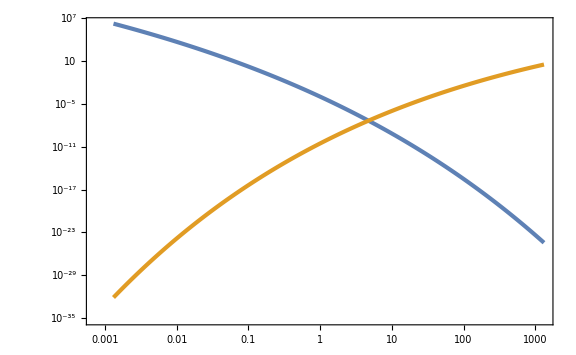

```mathematica
ListLogLogPlot[{fPBHPSListBlue,fPBHPSListRed}]
```

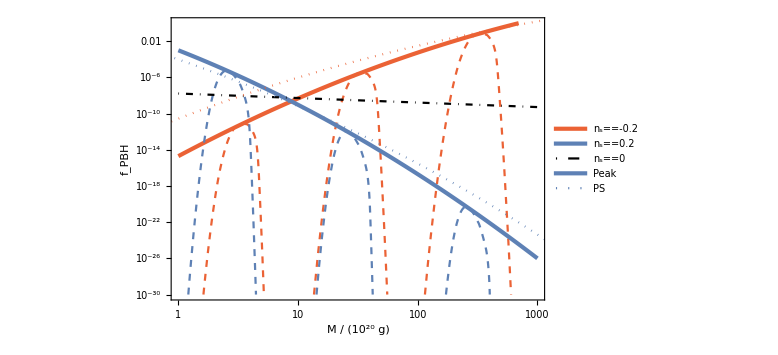

```mathematica
Show[LogLogPlot[{fPBHRedp[MM]UnitStep[50-MM],fPBHRed0[MM],fPBHRedm[MM],fPBHRedint[MM],fPBHBluep[MM],fPBHBlue0[MM],fPBHBluem[MM],fPBHBlueint[MM],fPBHflat[MM],0,0},{MM,1,10^3},PlotRange->{10^-30,1},PlotStyle->{{Color[4],Dashed},{Color[4],Dashed},{Color[4],Dashed},{Color[4],AbsoluteThickness[3]},{Color[1],Dashed},{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]},{Black,DotDashed},{Color[1],AbsoluteThickness[3]},{Color[1],Dotted}},FrameLabel->{{Subscript[f, PBH],None},{Row[{M," / (",Superscript[10,20]," g)"}],Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}]}},PlotLegends->Placed[LineLegend[{None,None,None,Subscript[n, "s"]==-0.2,None,None,None,Subscript[n, "s"]==0.2,Subscript[n, "s"]==0,"Peak","PS"},LegendFunction->(Framed[#1,Background->White]&),LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.22,0.2}]],ListLogLogPlot[{fPBHPSListRed,fPBHPSListBlue},PlotStyle->{{Color[4],Dotted},{Color[1],Dotted}}]]
```

### broken power-law

```mathematica
Quit[]
```

```mathematica
$Assumptions={r>0,sg>0,ks>0,n≥1,As>0,kW>0,x>0,mu>0,kappa>0,kappas>0};
```

```mathematica
calPz[k_,ks_,As_]=As((k/ks)^(3/2)UnitStep[ks-k]+(k/ks)^(-1/5)(1-UnitStep[ks-k]));
```

```mathematica
sigman[n_,kW_,As_,ks_]=√Integrate[k^(2n)calPz[k,ks,As] 1/k,{k,0,kW}]//Simplify
```

Piecewise[{{(√2 kW^(3/4+n) √(As/(3+4 n)))/ks^(3/4), ks≥kW}, {√((As (-17 ks^(2 n) kW^(1/5)+5 ks^(1/5) kW^(2 n) (3+4 n)))/(kW^(1/5) (-3+26 n+40 n^2))), True}}]

```mathematica
psin[n_,r_,kW_,kappas_]=1/sigman[2,kW,As,ks]^2 Integrate[k^(2n)Sin[k r]/(k r)calPz[k,ks,As] 1/k,{k,0,kW}]//Simplify
```

Piecewise[{{(11 kW^(-4+2 n) HypergeometricPFQ[{3/4+n},{3/2,7/4+n},-1/4 kW^2 r^2])/(3+4 n), ks≥kW}, {(209 ((5 ks^(2 n) HypergeometricPFQ[{-1/10+n},{3/2,9/10+n},-1/4 ks^2 r^2])/(1-10 n)+(5 ks^(1/5) kW^(-1/5+2 n) HypergeometricPFQ[{-1/10+n},{3/2,9/10+n},-1/4 kW^2 r^2])/(-1+10 n)+(2 ks^(2 n) HypergeometricPFQ[{3/4+n},{3/2,7/4+n},-1/4 ks^2 r^2])/(3+4 n)))/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

```mathematica
psin[1,r,kW,ks]//Simplify
psin[2,r,kW,ks]//Simplify
```

Piecewise[{{(11 HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kW^2 r^2])/(7 kW^2), ks≥kW}, {(209 (-5/9 ks^2 HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 ks^2 r^2]+5/9 (ks kW^9)^(1/5) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kW^2 r^2]+2/7 ks^2 HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 ks^2 r^2]))/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

Piecewise[{{HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kW^2 r^2], ks≥kW}, {(-55 ks^4 HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 ks^2 r^2]+55 (ks kW^19)^(1/5) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kW^2 r^2]+38 ks^4 HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 ks^2 r^2])/(-17 ks^4+55 (ks kW^19)^(1/5)), True}}]

```mathematica
gamma3[kW_,ks_]=sigman[3,kW,As,ks]^2/(sigman[2,kW,As,ks]sigman[4,kW,As,ks])//FullSimplify
Rb[kW_,ks_]=√3 sigman[3,kW,As,ks]/sigman[4,kW,As,ks]//Simplify
```

Piecewise[{{(√209)/15, ks≥kW}, {(19 √(143/3) (-17 ks^6+75 (ks kW^29)^(1/5)))/(145 √((-17 ks^4+55 (ks kW^19)^(1/5)) (-17 ks^8+95 (ks kW^39)^(1/5)))), True}}]

Piecewise[{{(√(19/5))/kW, ks≥kW}, {(√(741/145) √(-17 ks^6+75 (ks kW^29)^(1/5)))/(√(-17 ks^8+95 (ks kW^39)^(1/5))), True}}]

```mathematica
zetabar[r_,kW_,mu2_,kb_,ks_]=Simplify[mu2/(1-gamma3[kW,ks]^2)(psin[1,r,kW,ks]-1/3 Rb[kW,ks]^2 psin[2,r,kW,ks])]-mu2 kb^2 FullSimplify[sigman[2,kW,As,ks]/Simplify[sigman[4,kW,As,ks]gamma3[kW,ks](1-gamma3[kW,ks]^2)]](gamma3[kW,ks]^2 psin[1,r,kW,ks]-1/3 Rb[kW,ks]^2 psin[2,r,kW,ks])//Simplify
```

Piecewise[{{(15 mu2 (-121 (19 kb^2-15 kW^2) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kW^2 r^2]+133 (15 kb^2-11 kW^2) HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kW^2 r^2]))/(1232 kW^4), ks≥kW}, {(145 mu2 (-80465 ks^(11/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 ks^2 r^2]+80465 ks^(2/5) kW^(9/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kW^2 r^2]+9 (4598 ks^(11/5) (247 kb^2 (17 ks^(29/5)-75 kW^(29/5))+145 (-17 ks^(39/5)+95 kW^(39/5))) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 ks^2 r^2]+91 (55 ks^(21/5) (435 kb^2 (17 ks^(19/5)-55 kW^(19/5))+209 (-17 ks^(29/5)+75 kW^(29/5))) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 ks^2 r^2]+55 (209 (17 ks^(31/5) kW^(19/5)-75 ks^(2/5) kW^(48/5))+435 kb^2 (-17 ks^(21/5) kW^(19/5)+55 (ks kW^19)^(2/5))) HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kW^2 r^2]+38 ks^(21/5) (-435 kb^2 (17 ks^(19/5)-55 kW^(19/5))+209 (17 ks^(29/5)-75 kW^(29/5))) HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 ks^2 r^2]))))/(231 (3309628 ks^12-58975125 ks^(41/5) kW^(19/5)+131638650 ks^(31/5) kW^(29/5)-101866125 ks^(21/5) kW^(39/5)+39187500 ks^(2/5) kW^(58/5))), True}}]

```mathematica
zetax[x_,mu_,kappa_,kappas_]=zetabar[x/kW,kW,mu kW^2,kappa kW,kappas kW]//Simplify
```

Piecewise[{{-(15 mu (121 (-15+19 kappa^2) HypergeometricPFQ[{7/4},{3/2,11/4},-x^2/4]+133 (11-15 kappa^2) HypergeometricPFQ[{11/4},{3/2,15/4},-x^2/4]))/1232, kappas≥1}, {(145 mu (80465 (247 kappa^2 (-75+17 kappas^(29/5))+145 (95-17 kappas^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-x^2/4]+80465 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kappas^2 x^2]-9 (4598 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]+91 (435 kappa^2 (-55+17 kappas^(19/5))+209 (75-17 kappas^(29/5))) (55 HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+kappas^(19/5) (-55 HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]+38 HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2])))))/(231 (39187500-101866125 kappas^(19/5)+131638650 kappas^(29/5)-58975125 kappas^(39/5)+3309628 kappas^(58/5))), True}}]

```mathematica
CompactC[x_,mu_,kappa_,kappas_]=(1-(1+x D[zetax[x,mu,kappa,kappas], x])^2)/3//Simplify;
```

```mathematica
CompactC[1,1,1,0.1]
```

0.170489

```mathematica
xmcond[x_,kappa_,kappas_]=(D[zetax[x,mu,kappa,kappas], x]+x D[D[zetax[x,mu,kappa,kappas], x], x])x^2/mu//Simplify
```

Piecewise[{{15/64 (8 (-11+19 kappa^2) x Cos[x]-77 (-15+19 kappa^2) x HypergeometricPFQ[{7/4},{3/2,11/4},-x^2/4]+209 (-11+15 kappa^2) x HypergeometricPFQ[{11/4},{3/2,15/4},-x^2/4]+16 (77-114 kappa^2) Sin[x]), kappas≥1}, {(1653 (-522500 x Cos[x]+1072500 kappa^2 x Cos[x]-961350 kappa^2 kappas^(19/5) x Cos[x]+461890 kappas^(29/5) x Cos[x]+461890 kappa^2 kappas^(29/5) x Cos[x]-271150 kappas^(39/5) x Cos[x]+198 (247 kappa^2 (-75+17 kappas^(29/5))+145 (95-17 kappas^(39/5))) x HypergeometricPFQ[{9/10},{3/2,19/10},-x^2/4]+198 kappas^(9/5) (-247 kappa^2 (-75+17 kappas^(29/5))+145 (-95+17 kappas^(39/5))) x HypergeometricPFQ[{9/10},{3/2,19/10},-1/4 kappas^2 x^2]+5303375 kappas^(9/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-7132125 kappa^2 kappas^(9/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]+1616615 kappa^2 kappas^(38/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-949025 kappas^(48/5) x HypergeometricPFQ[{7/4},{3/2,11/4},-1/4 kappas^2 x^2]-7743450 x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+11818950 kappa^2 x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]-3653130 kappa^2 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+1755182 kappas^(29/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-x^2/4]+7743450 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-11818950 kappa^2 kappas^(19/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]+3653130 kappa^2 kappas^(38/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-1755182 kappas^(48/5) x HypergeometricPFQ[{19/10},{3/2,29/10},-1/4 kappas^2 x^2]-11207625 kappas^(19/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+17106375 kappa^2 kappas^(19/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]-5287425 kappa^2 kappas^(38/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+2540395 kappas^(48/5) x HypergeometricPFQ[{11/4},{3/2,15/4},-1/4 kappas^2 x^2]+5538500 Sin[x]-9223500 kappa^2 Sin[x]+4614480 kappa^2 kappas^(19/5) Sin[x]-2217072 kappas^(29/5) Sin[x]-1293292 kappa^2 kappas^(29/5) Sin[x]+759220 kappas^(39/5) Sin[x]-2575925 kappas^(4/5) Sin[kappas x]+3464175 kappa^2 kappas^(4/5) Sin[kappas x]+3464175 kappas^(14/5) Sin[kappas x]-5287425 kappa^2 kappas^(14/5) Sin[kappas x]+849082 kappa^2 kappas^(33/5) Sin[kappas x]-324258 kappas^(43/5) Sin[kappas x]))/(78375000-203732250 kappas^(19/5)+263277300 kappas^(29/5)-117950250 kappas^(39/5)+6619256 kappas^(58/5)), True}}]

```mathematica
FindRoot[xmcond[x,10^logk,kappas]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]/.{logk->0,kappas->1}
```

FindRoot::srect: Value Min[5.,3. 10.^(-1. logk)] in search specification {x,Min[3/10^logk,5]} is not a number or array of numbers.

{x→2.68032573992248743932667178385}

```mathematica
xmList=Flatten[ParallelTable[{logk,logks,Log10[x/.FindRoot[xmcond[x,10^logk,10^logks]==0,{x,Min[3/10^logk,5]},WorkingPrecision->30]]},{logk,-3,2,10^-1},{logks,-3,2,10^-1}],1];//AbsoluteTiming
```

{10.8442,Null}

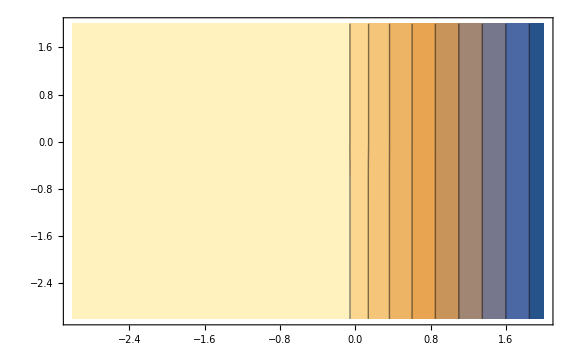

```mathematica
ListContourPlot[xmList]
```

```mathematica
xmint[kappa_,kappas_]=10^Interpolation[xmList][Log10[kappa],Log10[kappas]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3-Log[1000]/Log[10].

General::stop: Further output of N::meprec will be suppressed during this calculation.

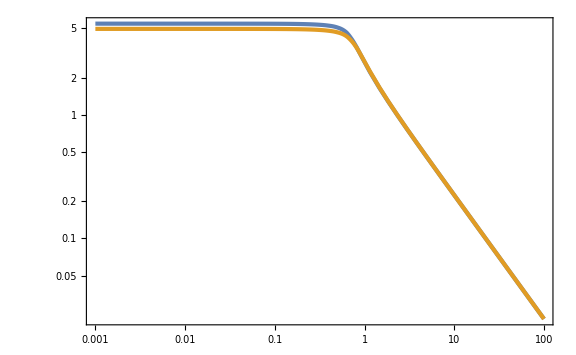

```mathematica
LogLogPlot[{xmint[kappa,10^-3],xmint[kappa,10^2]},{kappa,10^-3,10^2},PlotRange->Full]
```

```mathematica
Cmax[mu_,kappa_,kappas_]=CompactC[xmint[kappa,kappas],mu,kappa,kappas];
```

```mathematica
muthList=Flatten[ParallelTable[{logk,logks,Log10[mu/.Solve[Cmax[mu,10^logk,10^logks]==0.267,mu][[1]]]},{logk,-3,2,10^-1},{logks,-3,2,10^-1}],1];//AbsoluteTiming
```

{91.0746,Null}

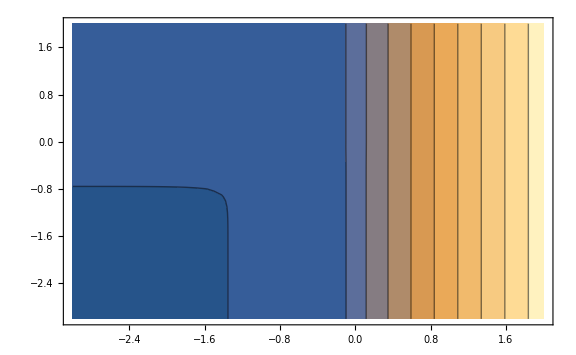

```mathematica
ListContourPlot[muthList]
```

```mathematica
muthint[kappa_,kappas_]=10^Interpolation[muthList][Log10[kappa],Log10[kappas]];
```

```mathematica
muthint[0.01,0.01]
```

0.099744

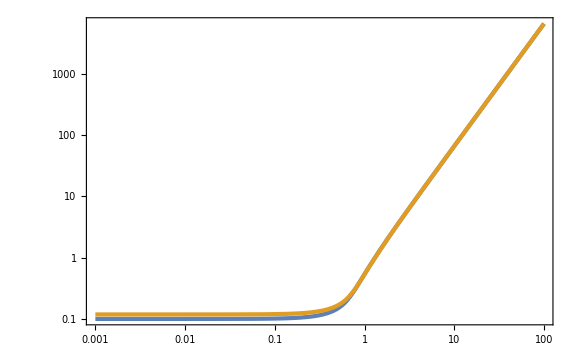

```mathematica
LogLogPlot[{muthint[kappa,10^-3],muthint[kappa,10^2]},{kappa,10^-3,10^2}]
```

```mathematica
gm[kappa_,kappas_]=zetax[xmint[kappa,kappas],mu,kappa,kappas]/mu;
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 3-Log[1000]/Log[10].

General::stop: Further output of N::meprec will be suppressed during this calculation.

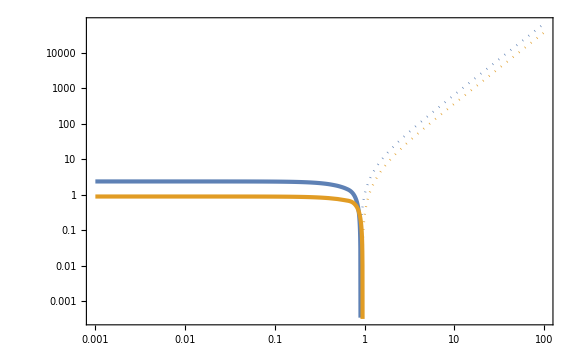

```mathematica
LogLogPlot[{gm[kappa,10^-3],-gm[kappa,10^-3],gm[kappa,10^2],-gm[kappa,10^2]},{kappa,10^-3,10^2},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted}}]
```

```mathematica
kappacList=ParallelTable[{10^logks,kappa/.FindRoot[gm[kappa,10^logks]==0,{kappa,1}]},{logks,-3,2,10^-1}];//AbsoluteTiming
```

{5.24423,Null}

```mathematica
kappacint[kappas_]=Interpolation[kappacList][kappas];
```

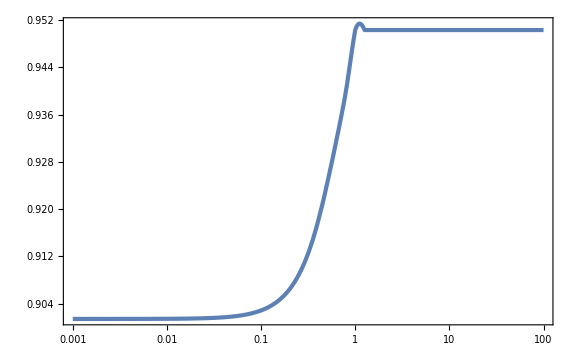

```mathematica
LogLinearPlot[kappacint[kappas],{kappas,10^-3,10^2}]
```

```mathematica
(6.4 10^-14)^-1
```

1.5625×10^13

```mathematica
sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)
```

(3 √(3/2))/(As kW^3)

```mathematica
sigman[4,kW,As]
```

(√As kW^4)/(2 √2)

```mathematica
sigman[2,kW,As]
```

(√As kW^2)/2

```mathematica
sigman[3,kW]^2/sigman[2,kW,As]^2
```

(2 kW^2)/3

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

-Graphics-

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

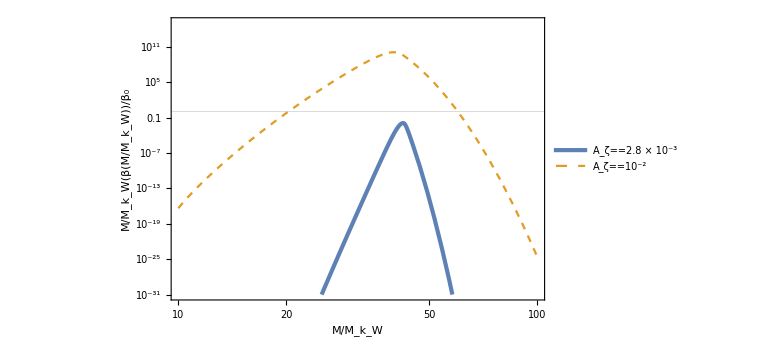

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

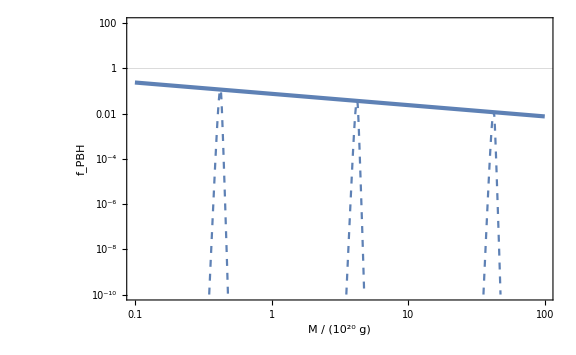

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

## non-Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=1/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//Simplify
```

1/3 (1-((5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

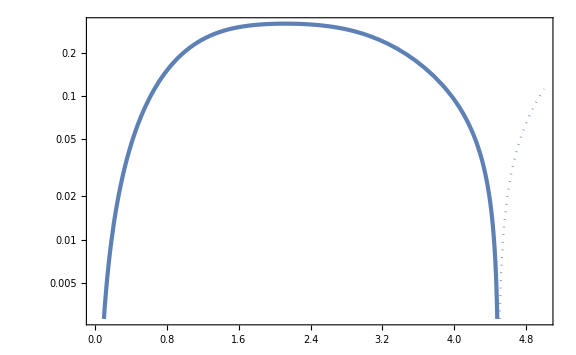

```mathematica
LogPlot[{CompactC[x,0.5,3],-CompactC[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

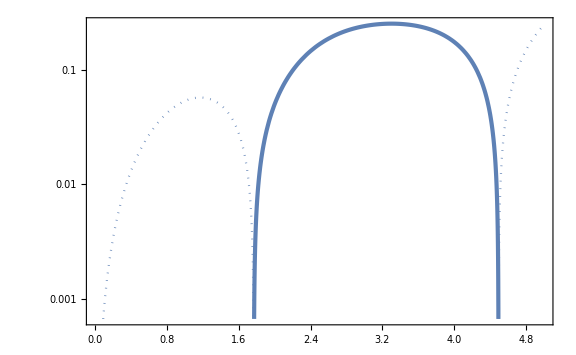

```mathematica
LogPlot[{CompactC[x,0.5,-3],-CompactC[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_,mu_,fNL_]=(5 x^3)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

6 fNL mu-5 x^2 Cos[x]+6 fNL mu (-1+x^2) Cos[2 x]+5 x Sin[x]-5 x^3 Sin[x]-9 fNL mu x Sin[2 x]

```mathematica
rmcond2[x_,mu_,fNL_]=5 x^2(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])

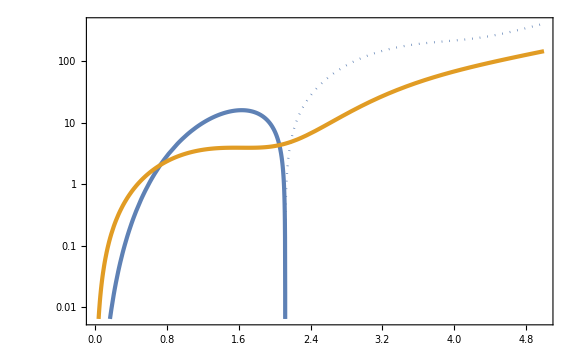

```mathematica
LogPlot[{-rmcond[x,0.5,3],rmcond[x,0.5,3],rmcond2[x,0.5,3],-rmcond2[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

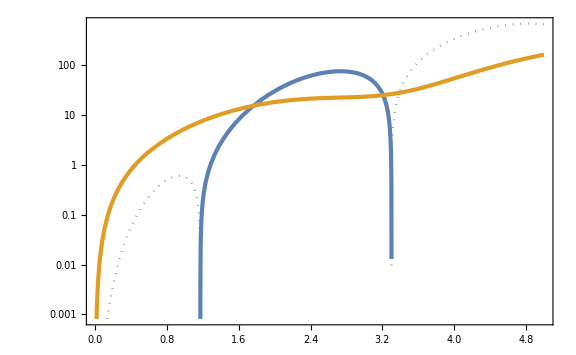

```mathematica
LogPlot[{-rmcond[x,0.5,-3],rmcond[x,0.5,-3],rmcond2[x,0.5,-3],-rmcond2[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[rmcond[x,0.5,3]==0,{x,3}]
```

{x→2.1157}

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3}]},{mufNL,-5/3,5/3,1/10}];
```

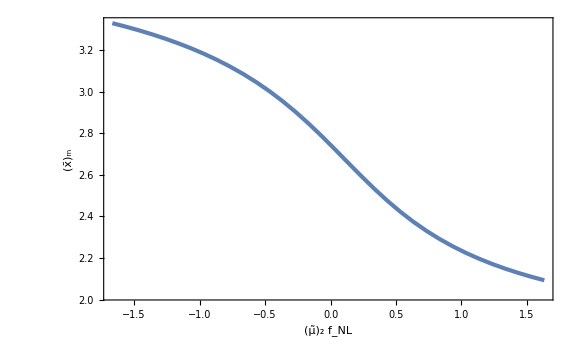

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Solve[CompactC[xmint[-5/3],mu,1/mu(-5/3)]==0.267,mu]
```

{{mu→0.537651},{mu→1.40366}}

```mathematica
muthList=Table[musol=mu/.Solve[CompactC[xmint[mufNL],mu,mufNL/mu]==0.267,mu][[1]];
{mufNL/musol,musol},{mufNL,-5/3,5/3,1/10}];
```

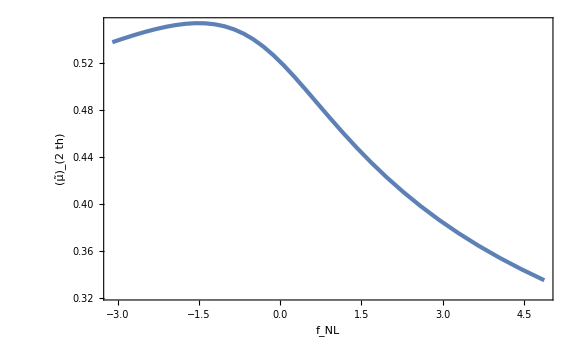

```mathematica
ListPlot[muthList,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2th]}]
```

```mathematica
fNLmin=First[muthList][[1]]
fNLmax=Last[muthList][[1]]
```

-3.0999

4.87679

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

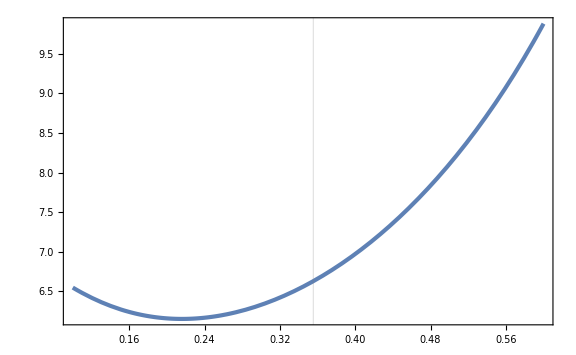

```mathematica
Plot[xmint[mu 4]^2 Exp[2zetabar[xmint[mu 4],mu,4]],{mu,0.1,0.6},GridLines->{{muthint[4]},None}]
```

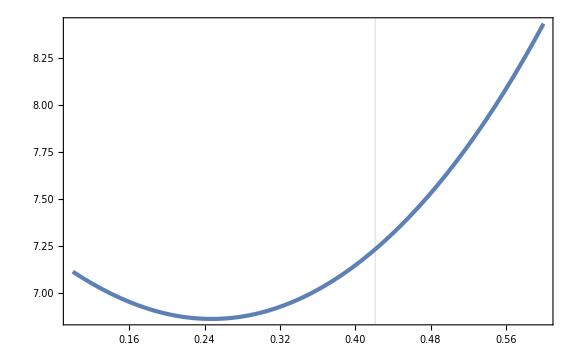

```mathematica
Plot[xmint[mu 2]^2 Exp[2zetabar[xmint[mu 2],mu,2]],{mu,0.1,0.6},GridLines->{{muthint[2]},None}]
```

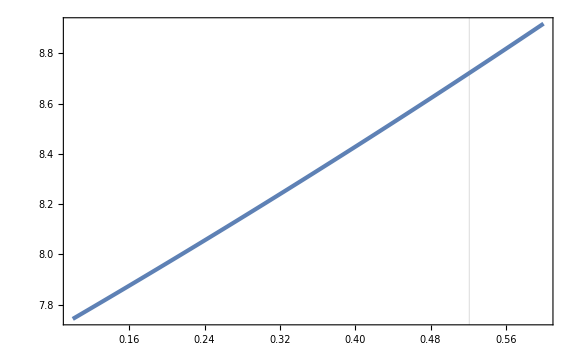

```mathematica
Plot[xmint[mu 0]^2 Exp[2zetabar[xmint[mu 0],mu,0]],{mu,0.1,0.6},GridLines->{{muthint[0]},None}]
```

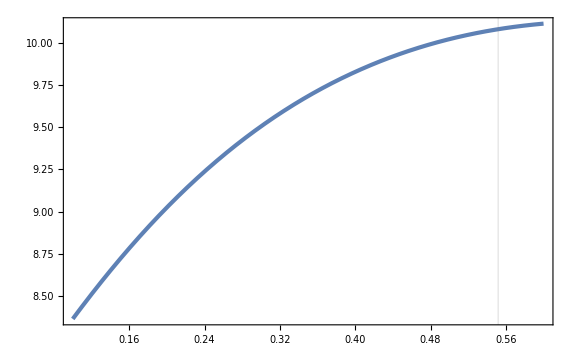

```mathematica
Plot[xmint[mu (-2)]^2 Exp[2zetabar[xmint[mu (-2)],mu,-2]],{mu,0.1,0.6},GridLines->{{muthint[-2]},None}]
```

```mathematica
dLogMdmu[mu_,fNL_]=D[Log[xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]], mu];
```

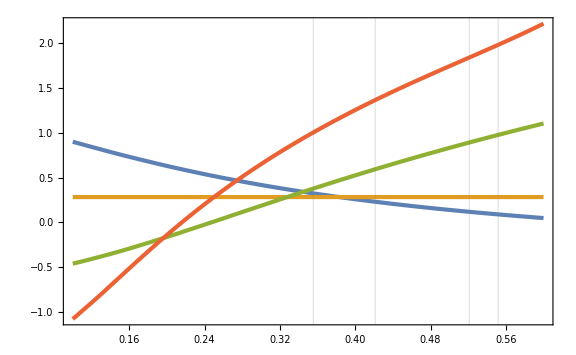

```mathematica
Plot[{dLogMdmu[mu,-2],dLogMdmu[mu,0],dLogMdmu[mu,2],dLogMdmu[mu,4]},{mu,0.1,0.6},GridLines->{{muthint[-2],muthint[0],muthint[2],muthint[4]},None}]
```

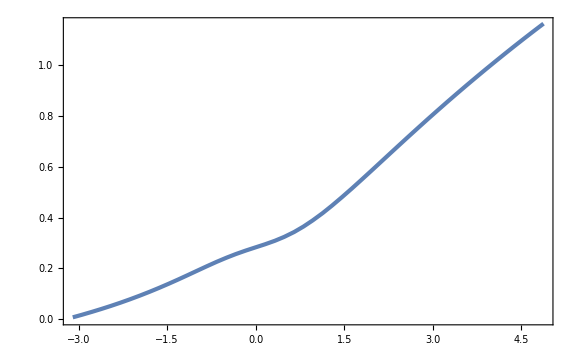

```mathematica
Plot[dLogMdmu[muthint[fNL],fNL],{fNL,fNLmin,fNLmax}(*,FrameLabel->{Subscript[f, NL],Subscript[Abs[Row[{"d log ",M}]/("d"Subscript[OverTilde[μ], 2])], Subscript[OverTilde[μ], 2]==Subscript[OverTilde[μ], 2th]]}*)]
```

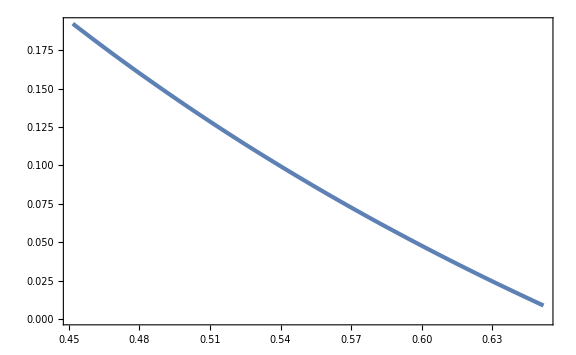

```mathematica
Plot[dLogMdmu[mu,-2],{mu,muthint[-2]-0.1,muthint[-2]+0.1}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)dLogMdmu[mu,fNL]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
muthint[-2]
```

0.551735

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.6,0]
```

7.70761×10^-8

```mathematica
fPBHListfNLm2=Table[{MoMks[mu,-2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,-2]},{mu,muthint[-2]-0.1,5/3 1/2,0.01}];
fPBHListfNL0=Table[{MoMks[mu,0],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,0]},{mu,muthint[0]-0.1,1,0.01}];
fPBHListfNLp2=Table[{MoMks[mu,2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,2]},{mu,muthint[2]-0.1,5/3 1/2,0.01}];
fPBHListfNLp4=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,muthint[4]-0.1,5/3 1/4,0.01}];
fPBHListfNLp4Ex=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,5/3 1/4,5/3 1/4+0.05,0.01}];
```

General::munfl: Exp[-708.863] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.043] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.64233} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66141} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66667} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

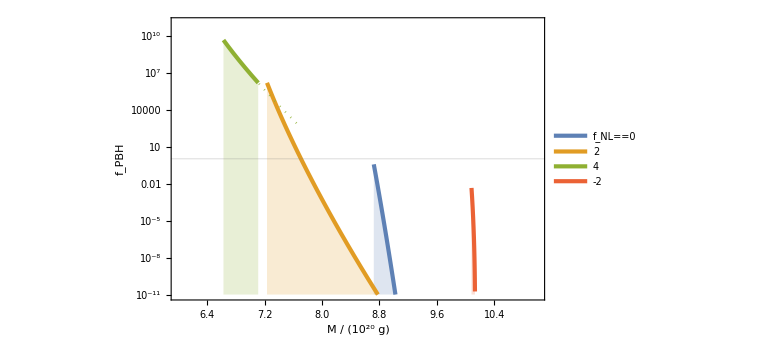

```mathematica
Show[ListLogPlot[{fPBHListfNL0,fPBHListfNLp2,fPBHListfNLp4,fPBHListfNLm2},PlotRange->{{6,11},{10^-11,10^11}},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==0,2,4,-2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.75}]],ListLogPlot[fPBHListfNLp4Ex,PlotStyle->{Color[3],Dotted}]]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,kL>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
sigma0[kW_,As_,kL_]=√(As Integrate[1,{logk,Log[kL],Log[kW]}])//Simplify
```

√(As Log[kW/kL])

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma1[kW_,kL_]=sigman[1,kW,As]^2/(sigma0[kW,As,kL]sigman[2,kW,As])//Simplify
gamma2[kW_,kL_]=sigman[2,kW,As]^2/(sigma0[kW,As,kL]sigman[4,kW,As])//Simplify
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

1/(√Log[kW/kL])

1/(√2 √Log[kW/kL])

(2 √2)/3

2/kW

```mathematica
DD[kW_,kL_]=1-gamma1[kW,kL]^2-gamma2[kW,kL]^2-gamma3^2+2gamma1[kW,kL] gamma2[kW,kL] gamma3
```

1/9-1/(6 Log[kW/kL])

```mathematica
zetaGbar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetaGx[x_,mu_,kappa_]=zetaGbar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
gx[x_,kappa_]=zetaGx[x,mu,kappa]/mu//Simplify
```

-(12 (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
g0[mu_,kappa_]=Limit[gx[x,kappa],{x->0}]
```

6-6 kappa^2

```mathematica
Manipulate[LogLinearPlot[gx[x,10^logk],{x,10^-2,10^2},PlotRange->Full],{logk,-0.1,0.1}]
```

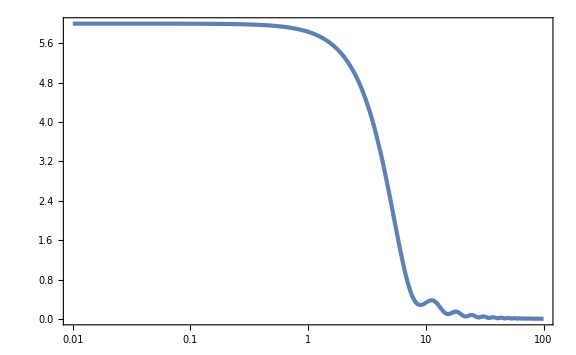

```mathematica
LogLinearPlot[gx[x,0],{x,10^-2,10^2}]
```

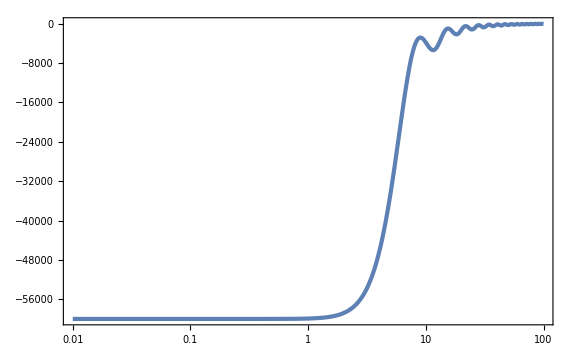

```mathematica
LogLinearPlot[gx[x,10^2],{x,10^-2,10^2}]
```

```mathematica
FindMaximum[{-gx[x,10^(-10^-2)],10^-2<x<6},{x,1}]
```

{0.944161,{x→4.33353}}

```mathematica
Max[FindMaxValue[{gx[x,10^-0.01],10^-2<x<6},{x,1}],FindMaxValue[{-gx[x,10^-0.01],10^-2<x<6},{x,1}]]
```

0.944161

```mathematica
gxMaxList=Table[{10^logk,Max[FindMaxValue[{gx[x,10^logk],10^-2<x<6},{x,1}],FindMaxValue[{-gx[x,10^logk],10^-2<x<6},{x,1}]]},{logk,-1,1,10^-2}];//AbsoluteTiming
```

{173.631,Null}

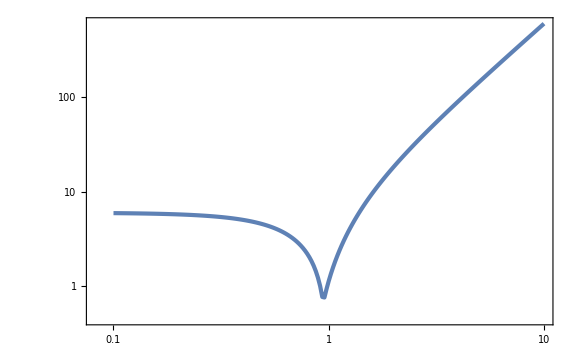

```mathematica
ListLogLogPlot[gxMaxList]
```

```mathematica
gxMaxInt[kappa_]=Interpolation[gxMaxList][kappa];
```

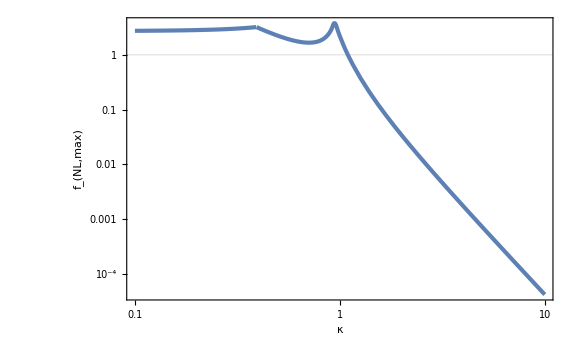

```mathematica
LogLogPlot[(3/5 Max[0.102,0.665 kappa^2]gxMaxInt[kappa])^-1,{kappa,0.1,10},FrameLabel->{κ,Subscript[f, NL,max]},GridLines->{None,{1}}]
```

```mathematica
zetabar[x_,mu_,kappa_,zetainf_,fNL_]=(1+6/5 fNL zetainf)zetaGx[x,mu,kappa]+3/5 fNL zetaGx[x,mu,kappa]^2//Simplify
```

1/(5 x^8)12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]) (-x^4 (5+6 fNL zetainf)+36 fNL mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))

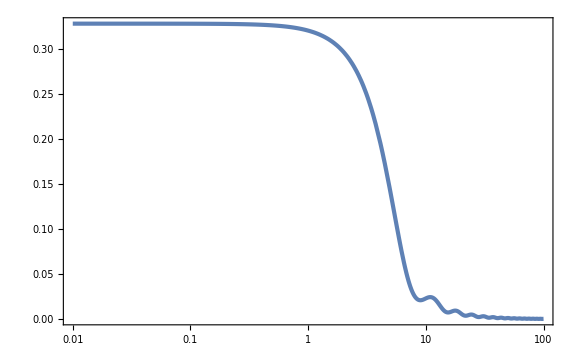

```mathematica
LogLinearPlot[zetabar[x,0.1,0.5,0,-1],{x,0.01,100},PlotRange->Full]
```

```mathematica
CompactC[x_,mu_,kappa_,zetainf_,fNL_]=(1-(1+x D[zetabar[x,mu,kappa,zetainf,fNL], x])^2)/3//Simplify
```

1/3 (1-(1-1/(5 x^8)24 mu (x Cos[x/2]-2 Sin[x/2]) (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2]) (-576 fNL mu+864 fNL kappa^2 mu-216 fNL mu x^2+288 fNL kappa^2 mu x^2-5 x^4-6 fNL x^4 zetainf+72 fNL mu (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-288 fNL (-2+3 kappa^2) mu x Sin[x]))^2)

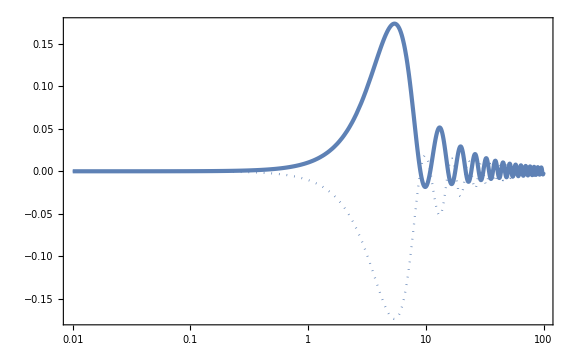

```mathematica
LogLinearPlot[{CompactC[x,0.1,0.5,0,-1],-CompactC[x,0.1,0.5,0,-1]},{x,0.01,100},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},PlotRange->Full]
```

```mathematica
xmcond[x_,mu_,kappa_,zetainf_,fNL_]=(5 x^9)/(12mu)(D[zetabar[x,mu,kappa,zetainf,fNL], x]+x D[D[zetabar[x,mu,kappa,zetainf,fNL], x], x])//Simplify
```

221184 fNL mu-663552 fNL kappa^2 mu+497664 fNL kappa^4 mu+93312 fNL mu x^2-264384 fNL kappa^2 mu x^2+186624 fNL kappa^4 mu x^2+640 x^4-960 kappa^2 x^4+5472 fNL mu x^4-14976 fNL kappa^2 mu x^4+10368 fNL kappa^4 mu x^4+60 x^6-80 kappa^2 x^6+768 fNL x^4 zetainf-1152 fNL kappa^2 x^4 zetainf+72 fNL x^6 zetainf-96 fNL kappa^2 x^6 zetainf+(5 x^4 (-128+52 x^2-x^4+2 kappa^2 (96-40 x^2+x^4))-6 fNL (12 mu (4096-320 x^2-280 x^4+3 x^6+8 kappa^4 (1152-144 x^2-73 x^4+x^6)-2 kappa^2 (6144-624 x^2-406 x^4+5 x^6))+x^4 (128-52 x^2+x^4-2 kappa^2 (96-40 x^2+x^4)) zetainf)) Cos[x]-72 fNL mu (-1024+1616 x^2-156 x^4+x^6-4 kappa^2 (-768+1230 x^2-129 x^4+x^6)+4 kappa^4 (-576+936 x^2-106 x^4+x^6)) Cos[2 x]-294912 fNL mu x Sin[x]+884736 fNL kappa^2 mu x Sin[x]-663552 fNL kappa^4 mu x Sin[x]-51264 fNL mu x^3 Sin[x]+140256 fNL kappa^2 mu x^3 Sin[x]-95040 fNL kappa^4 mu x^3 Sin[x]-640 x^5 Sin[x]+960 kappa^2 x^5 Sin[x]+3240 fNL mu x^5 Sin[x]-9936 fNL kappa^2 mu x^5 Sin[x]+7488 fNL kappa^4 mu x^5 Sin[x]+55 x^7 Sin[x]-90 kappa^2 x^7 Sin[x]-768 fNL x^5 zetainf Sin[x]+1152 fNL kappa^2 x^5 zetainf Sin[x]+66 fNL x^7 zetainf Sin[x]-108 fNL kappa^2 x^7 zetainf Sin[x]+147456 fNL mu x Sin[2 x]-442368 fNL kappa^2 mu x Sin[2 x]+331776 fNL kappa^4 mu x Sin[2 x]-48096 fNL mu x^3 Sin[2 x]+151056 fNL kappa^2 mu x^3 Sin[2 x]-118368 fNL kappa^4 mu x^3 Sin[2 x]+1404 fNL mu x^5 Sin[2 x]-5040 fNL kappa^2 mu x^5 Sin[2 x]+4464 fNL kappa^4 mu x^5 Sin[2 x]

```mathematica
xmcond2[x_,mu_,kappa_,zetainf_,fNL_]=(1+x D[zetabar[x,mu,kappa,zetainf,fNL], x])//Simplify
```

1-1/(5 x^8)24 mu (x Cos[x/2]-2 Sin[x/2]) (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2]) (-576 fNL mu+864 fNL kappa^2 mu-216 fNL mu x^2+288 fNL kappa^2 mu x^2-5 x^4-6 fNL x^4 zetainf+72 fNL mu (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-288 fNL (-2+3 kappa^2) mu x Sin[x])

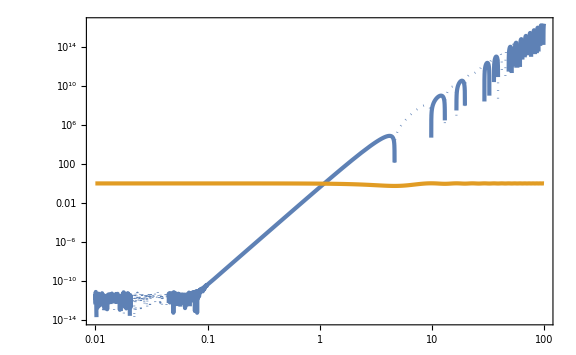

```mathematica
LogLogPlot[{-xmcond[x,0.1,0.5,0,1],xmcond[x,0.1,0.5,0,1],xmcond2[x,0.1,0.5,0,1],-xmcond2[x,0.1,0.5,0,1]},{x,0.01,100},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[xmcond[x,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->0.1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (4 (32+3 x^2-0.04 (12+x^2))+(-128+52 x^2-x^4+0.02 (96-40 Power[«2»]+x^4)) Cos[x]-x (128-11 x^2+0.06 (-32+3 Power[«2»])) Sin[x]==0) is less than WorkingPrecision (30.).

{x→5.3605653423668734007907946457}

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->30]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.23610391498593770655394732721

5.37014187909902279530303052317

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.24/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

-Graphics-

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==0.267,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

```mathematica
Solve[CompactC[5.37,mu,0]==0.267,mu]
```

{{mu→0.102313},{mu→0.26711}}

```mathematica
Normal[Series[mu/.Solve[Collect[Normal[Series[Simplify[CompactC[2.24/kappa,mu,kappa]],{kappa,∞,4}]],mu]==0.267,mu][[1]],{kappa,∞,2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.322681+0.2539/kappa^2+0.664695 kappa^2

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.102,0.665 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

-Graphics-

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

-Graphics-

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
(6.4 10^-14)^-1
```

1.5625×10^13

```mathematica
sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)
```

(3 √(3/2))/(As kW^3)

```mathematica
sigman[4,kW,As]
```

(√As kW^4)/(2 √2)

```mathematica
sigman[2,kW,As]
```

(√As kW^2)/2

```mathematica
sigman[3,kW]^2/sigman[2,kW,As]^2
```

(2 kW^2)/3

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

-Graphics-

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

-Graphics-

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-